## Transmittance PEDOT:PSS ~From Moritz

```mathematica
(*Set graphics style*) Needs["CustomTicks`"];
ticksx=LinTicks[100,1200,100,4,MajorTickLength->{.0,-0.025},MinorTickLength->{.0,-0.015},MajorTickStyle->{Thick,GrayLevel[0.1]},MinorTickStyle->{Thick,GrayLevel[0.1]}];
ticksy=LinTicks[0,1,0.2,2,MajorTickLength->{.0,-0.025},MinorTickLength->{.0,-0.015},MajorTickStyle->{Thick,GrayLevel[0.1]},MinorTickStyle->{Thick,GrayLevel[0.3]}];
```

Get::noopen: Cannot open CustomTicks`.

Needs::nocont: Context CustomTicks` was not created when Needs was evaluated.

```mathematica
(*Import all datafiles, one for each Sample*)
SetDirectory[NotebookDirectory[]];
Sample1=Drop[Import["Sample1.1.Sample.Raw.csv", "Table", FieldSeparators->"\\t"],1]; (*drop first item, the title*)
Sample2=Import["Sample2.Sample.Raw.csv", "Table", FieldSeparators->"\\t"];
Sample3=Import["Sample3.Sample.Raw.csv", "Table", FieldSeparators->"\\t"];
Sample4=Import["Sample4.Sample.Raw.csv", "Table", FieldSeparators->"\\t"];
Sample5=Import["Sample5.Sample.Raw.csv", "Table", FieldSeparators->"\\t"];
Sample6=Import["Sample6.Sample.Raw.csv", "Table", FieldSeparators->"\\t"];
```

```mathematica
(*Here I import generalized data into one long sheet*)Data=Table[Import["Sample*.Sample.Raw.csv","Table", FieldSeparators->"\\t"],6]
```

{1}
 |  |  |  |

```mathematica
(*Now I want to split that long list into n smaller ones where n=6*)
StringSplit["Data", "n"]
```

{Data}

```mathematica
(*some normalization function I do not understand
Sample1norm = Table[{Sample1[[i,1]],Sample1[[i,2]]-Sample4[[i,2]]},{i,1,Length[Sample11]}];
Sample2norm = Table[{Sample2[[i,1]],Sample2[[i,2]]-Sample3[[i,2]]},{i,1,Length[Sample2]}];
Sample3norm = Table[{Sample3[[i,1]],Tc[[i,2]]-ITO[[i,2]]},{i,1,Length[Tc]}]; *)
```

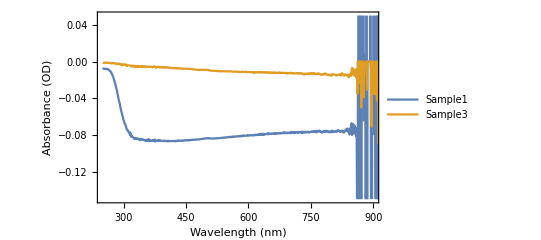

```mathematica
(*PlotFigure = ListPlot[{Pc1norm,Tcnorm},

PlotRange->{{250,900},{-0.15,0.05}},Joined->True,Frame->True,FrameStyle->Directive[GrayLevel[0.1],Thickness[0.005]],

FrameLabel->{"Wavelength (nm)","Absorbance (OD)"},

LabelStyle->{FontSize->16,FontFamily->"Helvetica",GrayLevel[0.1],Bold},

PlotLegends->Placed[{"Sample1","Sample3"},{0.8,0.8}],

ImageSize->400,AspectRatio->0.6]*)
```

```mathematica
SetDirectory[NotebookDirectory[ ]];
Export["Figure.png",Magnify[PlotFigure,2],Background->White];
```

```mathematica
(*Here I try plotting the raw data without normalization*)
PlotFigure = ListPlot[{Sample1, Sample2, Sample3, Sample4, Sample5, Sample6},

PlotRange->{{350,1200},{0,0.4}},Joined->True,Frame->True,FrameStyle->Directive[GrayLevel[0.1],Thickness[0.005]],

FrameLabel->{"Wavelength (nm)","Absorbance (OD)"},

LabelStyle->{FontSize->12,FontFamily->"Helvetica",GrayLevel[0.1],Bold},

PlotLegends->Placed[{"CIGS","CdTe", "Polysi", "IBCSi", "HITSi", "CIGSm"},{1,0.6}],

ImageSize->400,AspectRatio->0.6]
```

-Graphics-

```mathematica
export[name_,figure_]:=Export[name,Magnify[figure,2],Background->White];
```

```mathematica
export["soilabsorption.jpg",PlotFigure]
```

soilabsorption.jpg

```mathematica
(*So this is absorbance? Is it absorbance before I normalize it? what does that normalization (subtraction) actually do?*)
```

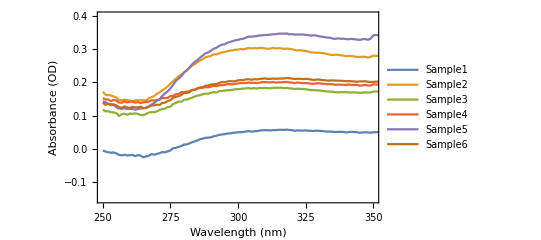

```mathematica
(*Zoom in on absorption peak*)
PlotFigure = ListPlot[{Sample1, Sample2, Sample3, Sample4, Sample5, Sample6},

PlotRange->{{250,350},{-0.15,0.4}},Joined->True,Frame->True,FrameStyle->Directive[GrayLevel[0.1],Thickness[0.005]],

FrameLabel->{"Wavelength (nm)","Absorbance (OD)"},

LabelStyle->{FontSize->16,FontFamily->"Helvetica",GrayLevel[0.1],Bold},

PlotLegends->Placed[{"Sample1","Sample2", "Sample3", "Sample4", "Sample5", "Sample6"},{0.8,0.8}],

ImageSize->400,AspectRatio->0.6]
```